RDML (.rdml, .rdm)

Importpaclet:ref/Import fully supports version 1.2. Versions 1.0 and 1.1 are partially supported, i.e., inasmuch as they overlap with version 1.2.

Background & Context

◼ MIME type: chemical/x-rdml+xml
◼ Real-time PCR Data Markup Language (RDML) is a structured and universal data standard for exchanging quantitative PCR (qPCR) data.
◼ RDML is an acronym for Real-time PCR Data Markup Language. | ◼ XML-based text format.
◼ The RDML format is developed and maintained by the RDML consortium (http://rdml.org).
◼ The RDML import functionality here provided is by Magno et al. (2017) (https://github.com/ramiromagno/rdml).

Installation

You need the package file rdml.m to import RDML files and the file RDML_v1_2_REC.xsd to be able to validate them against the XML schema. In addition, you will also need this notebook to access this documentation: RDML.nb.

To install all the required files clone the github repository: https://github.com/ramiromagno/rdml. Alternatively, download and extract the zip archive: https://github.com/ramiromagno/rdml/archive/master.zip.

Import

Importpaclet:ref/Import["file.rdml"] reads an RDML file and returns a Datasetpaclet:ref/Dataset expression; this expression is a nested structure of lists and associations whose hierarchy reflects that of the RDML schema.

Importpaclet:ref/Import["file",{"RDML",elem,…}] imports the specified top-element from an RDML file.

Elements

Top-level RDML Importpaclet:ref/Import elements:

| "version" | RDML schema version
       | "dateMade" | date and time stamp of the creation of the file
       | "dateUpdated" | date and time stamp of the last update of the file
       | "id" | publisher and id to the RDML file
       | "experimenter" | list of experimenters involved in the experiments reported
       | "documentation" | multi-purpose documentation system
       | "dye" | information regarding the fluorescent chemical compounds used as dyes for the real-time monitoring of the qPCR reaction
       | "sample" | sample describes either standard samples used in a dilution series or different biological sources and/or conditions/treatments performed on biological material
       | "target" | target is defined by the primer (and probe) mix added to the sample to specifically amplify the target sequence (amplicon)
       | "thermalCyclingConditions" | temperature and time steps taken by a thermocycler in order to amplify the DNA
       | "experiment" | data collected during one (or more) qPCR runs

Import Options

Import options:

| "ValidateAgainstXSD" | False | whether to validate file against RDML schema before importing
       | "Compressed" | Automatic | whether to assume that the file is a compressed archive
       | "Dataset" | True | whether to return a Dataset structure expression

### ValidateAgainstXSD

By default, the importer will not attempt to validate the file against the XML schema. If the file to be imported is not compliant with version 1.2, it will still attempt to import inasmuch as it is compatible with version 1.2.

However, to check if the file to be imported complies with the XML Schema, set the option ValidateAgainstXSD->True. If the file fails to be validated, a warning is issued and Import returns $Failed:

```mathematica
Import["https://github.com/ramiromagno/rdml/blob/master/datasets/QPCRCourseApril2015_plate_1_.rdml?raw=true","RDML","ValidateAgainstXSD"->True]
```

Private`import::xsderr: Could not validate the file /tmp/m00003619601/QPCRCourseApril2015_plate_1_.rdml against /home/rmagno/code/mathematica/pkg/rdml/RDML_v1_2_REC.xsd: cvc-enumeration-valid: Value 'LinRegPCR, threshold per target' is not facet-valid with respect to enumeration '[automated threshold and baseline settings, manual threshold and baseline settings, second derivative maximum, other]'. It must be a value from the enumeration..

$Failed

Conversely, if no errors are detected, the data is simply returned:

```mathematica
Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML","ValidateAgainstXSD"->True]
```

Dataset[<>]

### Compressed

According to the RDML Consortium guidelines, the XML file containing the RDML compliant data should be stored in a file named rdml_data.xml. This file should be compressed into a pkzip compatible archive. The archive can be freely named, however instead of holding the .zip extension, it should hold the .rdml (preferably) or .rdm extension. In addition, RDML compatible software should be able to read compressed .rdml or .rdm files, as well as uncompressed .xml files.

By default the importer tries to determine if the file is compressed or not (default option Compressed->Automatic) by checking if the first two bytes of the file correspond to the ASCII string PK.

For instance, if you'd want to manually check if some file is a pkzip compatible archive, you could run:

```mathematica
Import["https://github.com/ramiromagno/rdml/blob/master/datasets/QPCRCourseApril2015_plate_1_.rdml?raw=true",{"Byte",{1,2}}]//FromCharacterCode
```

PK

The following three Import calls are all equivalent for a compressed RDML file:

```mathematica
file="https://github.com/ramiromagno/rdml/blob/master/datasets/QPCRCourseApril2015_plate_1_.rdml?raw=true";
Import[file, "RDML"]
Import[file,"RDML","Compressed"->Automatic]
Import[file,"RDML","Compressed"->True]
```

Dataset[<>]

Dataset[<>]

Dataset[<>]

Explicitly forcing the importer to assume that the file is not compressed (when it actually is) will result in $Failed with XML-related parsing errors:

```mathematica
Import[file,"RDML","Compressed"->False]
```

XML`Parser`XMLGet::prserr: TranscodingException: An invalid multi-byte source text sequence was encountered at Line: 1 Character: 1 in /tmp/m00004819601/QPCRCourseApril2015_plate_1_.rdml.

Import::fmterr: Cannot import data as XML format.

$Failed

The importer will run smoothly on an uncompressed file (rdml_data.xml is QPCRCourseApril2015_plate _ 1_. rdml uncompressed):

```mathematica
Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rdml_data.xml?raw=true","RDML","Compressed"->False]
```

Dataset[<>]

If the file extension is not .rdml or .rdm, then the file type is mandatory, otherwise Import will read the input file as XML and return a XMLObject expression:

```mathematica
Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rdml_data.xml?raw=true"]
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0]},XMLElement[rdml,{1,1},{XMLElement[dateMade,{},{2015-06-03T13:13:41}],42,XMLElement[experiment,{id→…},{XMLElement[run,{id→…},{XMLElement[backgroundDeterminationMethod,{},{LinRegPCR, constant}],289,XMLElement[react,{id→288},{XMLElement[sample,{id→34},{}],XMLElement[1]}]}]}]}],{}]
 |  |  |  |

### Dataset

By default, the expression returned after import is a Dataset expression. Setting Dataset-> False returns the underlying RDML data explicitly as a nested structure of associations and lists:

```mathematica
Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML","Dataset"->False]//Short
```

<|version→1.2,«9»,experiment→<|All Wells→<|description→A1-H12,«1»,run→<|Amp Step 3_SYBR→<|«1»|>|>|>|>|>

## Import Usage Examples

Import an RDML file from one of the provided datasets from the github repository of this importer:

```mathematica
Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML"]
```

Dataset[<>]

Get the schema version of this RDML file:

```mathematica
Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true",{"RDML", "version"}]
```

1.2

Get the identification of the publisher of this RDML file:

```mathematica
Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true",{"RDML", "id"}]
```

Dataset[<>]

Import the experimenters:

```mathematica
Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true",{"RDML", "experimenter"}]
```

Dataset[<>]

## RDML Dataset

### schema version

The version element indicates the RDML Schema version of the file. This element can be easily retrieved from the Dataset object:

```mathematica
rpa=Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML"];
rpa["version"]
```

1.2

Since its release, the RDML standard has been revised twice: versions 1.1 and 1.2. Although this importer has been designed to fully support version 1.2, in practice, since version 1.2 Schema specification significantly overlaps with previous versions, this package can import RDML files from those previous versions (to the extent that they overlap with version 1.2).

Importing files from versions other than 1.2 results in a warning, yet most data is often successfully imported:

```mathematica
Import["https://github.com/ramiromagno/rdml/blob/master/datasets/1507AA03.rdml?raw=true","RDML"]
```

Private`xmlObjectToExpression::version: RDML file version is 1.0 but only version 1.2 is supported. The parsing will proceed presuming version 1.2, hence some data might be not imported.

Dataset[<>]

### dateMade

The element dateMade indicates the date and time stamp of the creation of the file:

```mathematica
rpa=Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML"];
rpa["dateMade"]
```

Mon 22 Apr 2013 20:29:44GMT+1.

### dateUpdated

The element dateUpdated indicates the date and time stamp of the last update of the file.:

```mathematica
rpa=Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML"];
rpa["dateUpdated"]
```

Tue 30 Apr 2013 12:08:11GMT+1.

### id

Use the id element to show all ids. Each id can be used to assign a publisher and a serial number to the RDML file. Additionally, an MD5Hash can also be included.

```mathematica
rpa=Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML"];
rpa["id"]
```

Dataset[<>]

### experimenter

The experimenter element contains a list of researchers and their info (in this case only one):

```mathematica
rpa=Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML"];
rpa["experimenter"]
```

Dataset[<>]

Internally this is represented as an Association. The key in this Association corresponds to the XML id attribute (in this example "rpa") from the original RDML file, which can be used by other elements to link here:

```mathematica
rpa["experimenter"]//Normal
```

<|rpa→<|firstName→Raquel,lastName→Andrade,email→rgandrade@ualg.pt,labName→CBMR,labAddress→Centre for Biomedical Research, University of Algarve, 8005-139 Faro, Portugal|>|>

To retrieve all information related to one particular experimenter, one can either use the key (XML id):

```mathematica
rpa["experimenter","rpa"]
```

Dataset[<>]

Or pick out the corresponding Part:

```mathematica
rpa["experimenter",1]
```

Dataset[<>]

### documentation

The documentation element constitutes the multi-purpose documentation system from the RDML file. This element is a text field with an unique id (translated to a key in an Association).
From many places in the RDML file, a reference can be made to these documentation elements, making it versatile and allowing the free annotation of the elements.
To retrieve all documentation elements:

```mathematica
rpa=Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML"];
rpa["documentation"]
```

Dataset[<>]

In this file there is only one such element, whose contents pertain to the genome assembly version used to retrieve the genomic information on the HoxB gene cluster:

```mathematica
rpa["documentation",1]
```

Dataset[<>]

Whose text sub-element contains:

```mathematica
rpa["documentation",1,"text"]
```

The genomic information for the HoxB cluster is based on the Gallus gallus (chick) genome assembly version 2.1 (WASHUC2), as performed by the Genome Sequencing Center (http://genome.wustl.edu) at the Washington University School of Medicine, St. Louis.

### dye

The dye element contains information regarding the fluorescent chemical compounds used as dyes for the real-time monitoring of the qPCR reaction.
To show all dyes:

```mathematica
rpa=Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML"];
rpa["dye"]
```

Dataset[<>]

### sample

The sample element contains all samples used. It may describe standard samples used in a dilution series, but it will often describe different biological sources and/or conditions/treatments performed on biological material.
To inspect the different samples:

```mathematica
rpa=Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML"];
rpa["sample"]
```

Dataset[<>]

Check information associated with one particular sample, e.g. "R-MoH9":

```mathematica
rpa["sample","R-MoH9"]
```

Dataset[<>]

Each sample can have a type: unkn (unknown sample), ntc (non template control), nac (no amplification control), std (standard sample), ntp (no target present), nrt (minusRT, negative for Reverse Transcription), pos (positive control) or opt (optical calibrator sample).

```mathematica
rpa["sample",All,"type"]
```

Dataset[<>]

Inspect the description of all samples:

```mathematica
rpa["sample",All,"description"]
```

Dataset[<>]

### target

The target element contains all targets. A target is defined by the primer (and probe) mix added to the sample to specifically amplify the target sequence (amplicon).

```mathematica
rpa=Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML"];
rpa["target"]
```

Dataset[<>]

Examine all amplicon sequences:

```mathematica
rpa["target",All,"sequences","amplicon","sequence"]
```

Dataset[<>]

Inspect the forward and reverse primers:

```mathematica
rpa["target",All,"sequences",{"forwardPrimer","reversePrimer"},"sequence"]//Dataset
```

Dataset[<>]

The xRef subelement relates the targets to an external database:

```mathematica
rpa["target",All,"xRef",1]
```

Dataset[<>]

### thermalCyclingConditions

The thermalCyclingConditions element describes the temperature and time steps taken by a thermocycler in order to amplify the DNA. It can be used to describe alternative cycling programs (e.g., a regular PCR or a cDNA synthesis program).
Show the temperature protocol description:

```mathematica
rpa=Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML"];
rpa["thermalCyclingConditions",1,"description"]
```

Temperature protocol: melting temperature is 95 Celsius degrees; annealing temperature is 55 Celsius degrees; total number of cycles: 61 (60 repeats after first step). Melting curve performed at the end of amplification: 65 thru 95 Celsius degrees (step: 0.5 degrees per 5 seconds).

Examine the various steps that compose the actual program:

```mathematica
rpa["thermalCyclingConditions",1,"step"]
```

Dataset[<>]

### experiment

The experiment element contains the data collected during one (or more) qPCR runs, where each run contains one or more qPCR reactions. Each reaction incorporates one sample (which is referred to by its id) and one or more data elements (one for each target (also referred by its id)). Multiple data elements are only required for a multiplex reaction, in which several targets are simultaneously measured (using different fluorescent dyes). If the reactions are measured in different runs, the data should be stored as separate runs.
Check the first run in the experiment element:

```mathematica
rpa=Import["https://github.com/ramiromagno/rdml/blob/master/datasets/rpa.rdml?raw=true","RDML"];
rpa["experiment",1,"run",1]
```

Dataset[<>]

This run holds various details, including specifics about the hardware (instrument element) as well as details about the software that collected the data (dataColletionSoftware); documentation, experimenter and thermalCyclingConditions elements should have id references to elements previously defined. The backgroundDeterminationMethod and cqDetectionMethod elements include relevant information about the mathematical analysis of the qPCR amplification curves. The pcrFormat element allows downstream analysis software to display the data according to the qPCR instrument run format. Finally, the react element contains the actual data pertaining to the qPCR reactions, containing a list of qPCR reactions, each consisting of two subelements: sample and data.

```mathematica
rpa["experiment",1,"run",1,"react"]
```

Dataset[<>]

Examine the summary of cq values for all reactions of sample "R-MoH9":

```mathematica
cq["R-MoH9"]=rpa["experiment",1,"run",1,"react",Select[#sample=="R-MoH9"&],"data",1,{"tar","cq"}]
```

Dataset[<>]

The adp and mdp subelements contain the amplification and melting data, respectively.
Plot amplification curves for all reactions of sample "R-MoH9":

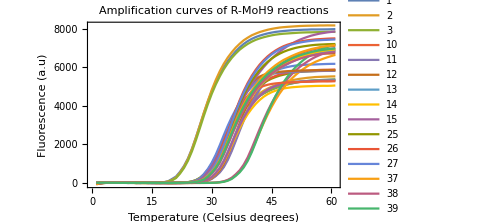

```mathematica
amplificationData["R-MoH9"]=rpa["experiment",1,"run",1,"react",Select[#sample=="R-MoH9"&],"data",1,"adp",All,{"cyc","fluor"}];
ListPlot[amplificationData["R-MoH9"],Joined->True,Frame->True,PlotLabel->"Amplification curves of R-MoH9 reactions",FrameLabel->{"Temperature (Celsius degrees)","Fluorescence (a.u)"},ImageSize->Medium]
```

Plot melting curves for all reactions of sample "R-MoH9":

```mathematica
meltingData["R-MoH9"]=rpa["experiment",1,"run",1,"react",Select[#sample=="R-MoH9"&],"data",1,"mdp",All,{"tmp","fluor"}];
```

To highlight the melting temperature, calculate the negative of the derivative of the fluorescence with respect to temperature:

```mathematica
meltingData2["R-MoH9"]=Values/@meltingData["R-MoH9"]//Normal//Values;
```

```mathematica
interpolatedMeltingData["R-MoH9"]=Interpolation/@meltingData2["R-MoH9"];
```

```mathematica
interpolatedDerMeltingData["R-MoH9"]=(-D[#[t],t])&/@interpolatedMeltingData["R-MoH9"];
```

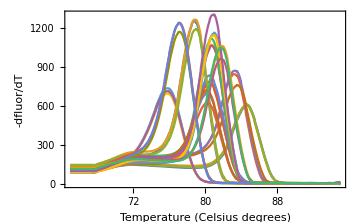

```mathematica
Plot[interpolatedDerMeltingData["R-MoH9"],{t,65,95},PlotRange->All,Frame->True,FrameLabel->{"Temperature (Celsius degrees)","-dfluor/dT"},ImageSize->Medium]
```